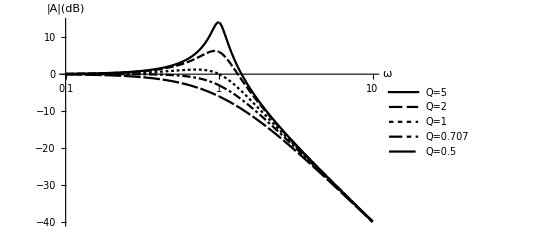

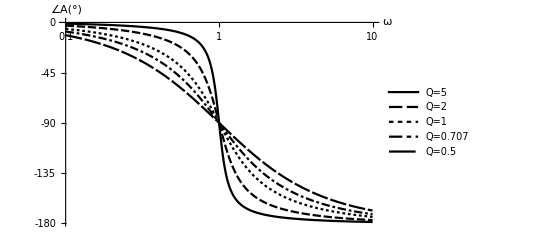

```mathematica
G[s_,Q_]:=1/(1+1/Q s+s^2);
Q={0.5,0.707,1,2,5};
LogLinearPlot[
{
20Log10[Abs[G[ⅈ o,Q[[5]]]]],
20Log10[Abs[G[ⅈ o,Q[[4]]]]],
20Log10[Abs[G[ⅈ o,Q[[3]]]]],
20Log10[Abs[G[ⅈ o,Q[[2]]]]],
20Log10[Abs[G[ⅈ o,Q[[1]]]]]
},
{o,0.1,10},
PlotTheme->"Monochrome",
AxesLabel->{"ω","|A|(dB)"},
PlotLegends->{"Q=5","Q=2","Q=1","Q=0.707","Q=0.5"}
]
LogLinearPlot[
{
Arg[G[ⅈ o,Q[[5]]]]*180/π,
Arg[G[ⅈ o,Q[[4]]]]*180/π,
Arg[G[ⅈ o,Q[[3]]]]*180/π,
Arg[G[ⅈ o,Q[[2]]]]*180/π,
Arg[G[ⅈ o,Q[[1]]]]*180/π
},
{o,0.1,10},
PlotTheme->"Monochrome",
Ticks->{Automatic,{0,-45,-90,-135,-180}},
AxesLabel->{"ω","∠A(°)"},
PlotLegends->{"Q=5","Q=2","Q=1","Q=0.707","Q=0.5"}
]
```